```mathematica
files=FileNames["*.tab"];
datas=Drop[Import[#],1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data=Transpose[{ch1s,ch2s}];
```

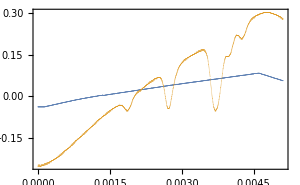
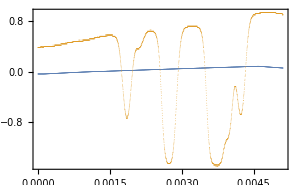
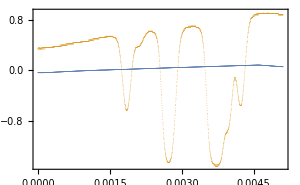
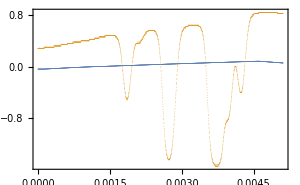
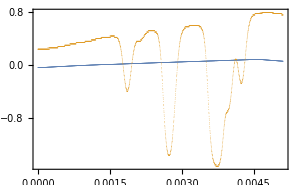
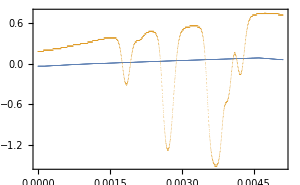
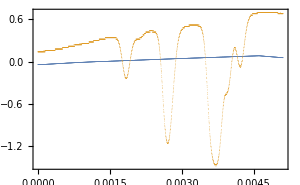
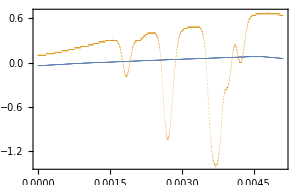

```mathematica
ListPlot[#, PlotRange->All, Frame->True, ImageSize->300, PlotStyle->{PointSize[0.0001]}]&/@ data
```

FittedModel[-2.+1.0338 ⅇ^(-4.80937×10^8 (-«22»+x)^2)+3124.21 x]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -2. | 0.136776 | -14.6225 | 6.60494×10^-35
b | 3124.21 | 260.96 | 11.972 | 4.01027×10^-26
A | 1.0338 | 0.0284147 | 36.3824 | 9.45652×10^-99
c | 0.622682 | 0.00047876 | 1300.61 | 5.92400741194597×10^-457
σ | 0.0455991 | 0.00105344 | 43.286 | 3.06611×10^-114

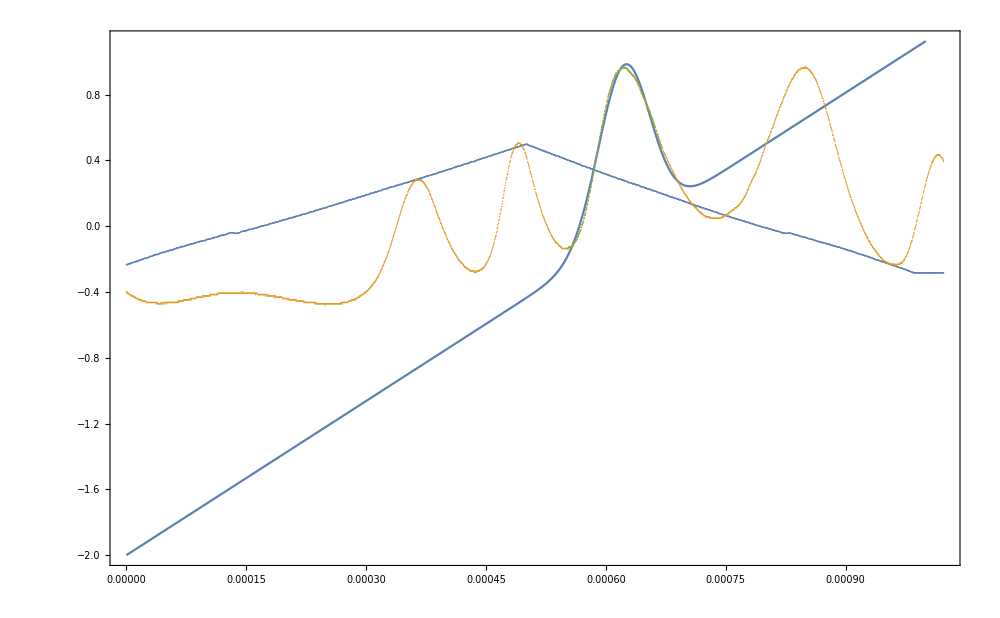

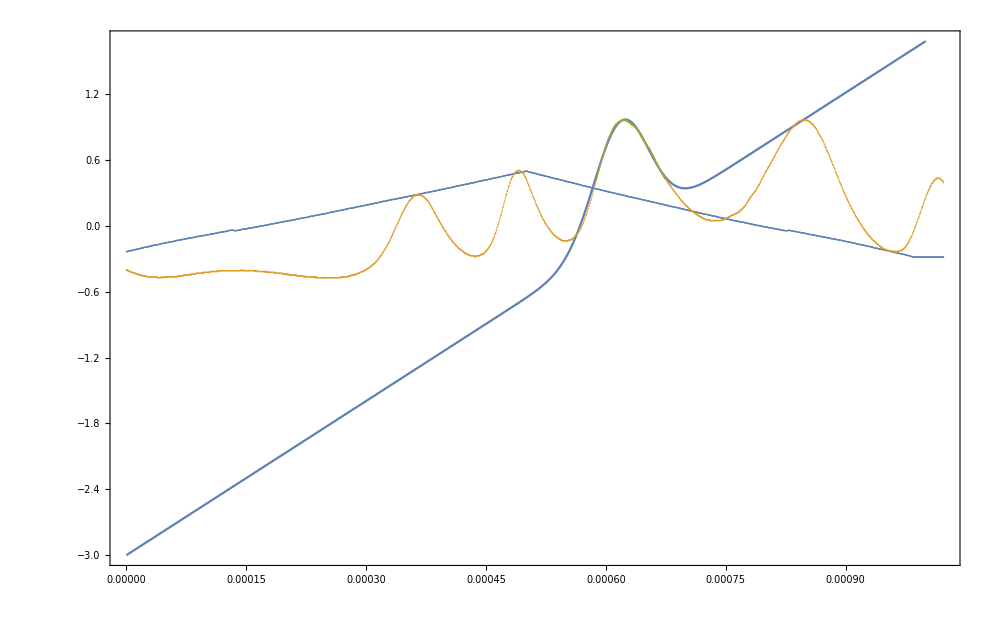

```mathematica
fitmin = 0.00055;
fitmax = 0.00067;
fitData = Select[data[[37, 2]], #[[1]] ≥fitmin && #[[1]] ≤ fitmax&];
nlm = NonlinearModelFit[fitData, {a + b x + A Exp[- ((x-c*10^-3)/(σ * 10^-3))^2], a < 0, a > -2, b > 0, σ > 0, A < 2, A > 0}, {{a, -0.6}, {b, 1000}, {A, 1}, {c, 0.625}, {σ, 0.06}}, x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm], {x, 0, 0.001}, PlotRange->All, ImageSize->1000, Frame->True, Axes->False], ListPlot[Append[data[[37]], fitData],PlotStyle->{PointSize[0.001]}]]
```

```mathematica
mdata = Transpose[{{0.0005481,-0.131},{0.0007405,0.05336}}];
Differences[mdata[[2]]]/Differences[mdata[[1]]]
```

{958.212}

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.